# Fonctions de carré sommable

### Exemple 1

#### Forme non normée

```mathematica
f[x_]:=ⅇ^(-x^2/2) ;
```

```mathematica
∫_(-∞)^(+∞) Abs[f[x]]^2 ⅆx
```

√π

#### Forme normée

```mathematica
f[x_]:=π^(-1/4)ⅇ^(-x^2/2) ;
```

```mathematica
∫_(-∞)^(+∞) Abs[f[x]]^2 ⅆx
```

1

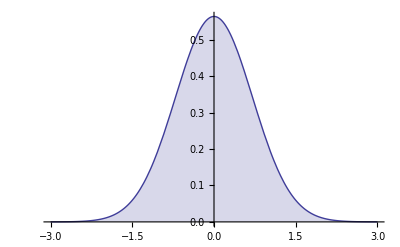

```mathematica
Plot[Abs[f[x]]^2,{x,-3,3},Filling->Axis]
```

### Exemple 2

#### Forme non normée

```mathematica
f[x_]=ⅇ^(-α (x-Subscript[x, 0])^2)/.α->4/.Subscript[x, 0]->2
```

ⅇ^(-4 (-2+x)^2)

```mathematica
w[x_] = 1;
```

```mathematica
∫_(-∞)^(+∞) Abs[f[x]]^2 ⅆx
```

(√(π/2))/2

#### Forme normée

```mathematica
f[x_]:=(8/π)^(1/4)ⅇ^(-α (x-Subscript[x, 0])^2)/.α->4/.Subscript[x, 0]->2
```

```mathematica
∫_(-∞)^(+∞) Abs[f[x]]^2 ⅆx
```

1

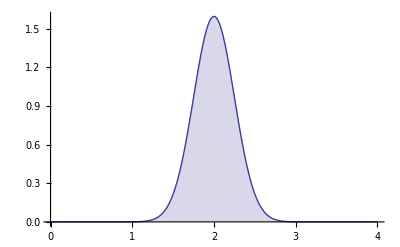

```mathematica
Plot[Abs[f[x]]^2,{x,0,4},Filling->Axis,PlotRange->All]
```

### Exemple 3

#### Forme non normée

```mathematica
f[x_]:=Sin[π x];
```

```mathematica
∫_0^1 Abs[f[x]]^2 ⅆx
```

1/2

#### Forme normée

```mathematica
f[x_]:=√2 Sin[π x];
```

```mathematica
∫_0^1 Abs[f[x]]^2 ⅆx
```

1

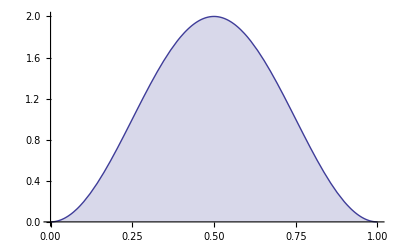

```mathematica
Plot[Abs[f[x]]^2,{x,0,1},Filling->Axis]
```